# Unfolding Pattern Search

## Global Functions

```mathematica
ClearAll["Global`*"]
MyAdjacencyMatrix[G0_]:=Module[{g=G0},n=Length[VertexList[g]];A=ConstantArray[0,{n,n}];
For[x=1,x≤n,x++,V=VertexList[NeighborhoodGraph[g,x,1]];For[y=1,y≤Length[V],y++,A[[x,V[[y]]]]=1]];
A-IdentityMatrix[n]
]

Smash[G0_,S0_]:=Module[{G=G0,S=S0,V,A,Sbar},
(*Get the adjacency matrix of the graph*)
A=AdjacencyMatrix[G];
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]

SmashAdj[A0_,G0_,S0_]:=Module[{A=A0,G=G0,S=S0,V,Sbar},
(*Get the adjacency matrix of the graph*)
V=VertexList[G];
(*Map vertex labels to matrix indices*)
S=Flatten[Position[V,#]&/@S0];
Sbar=Complement[Range[Length[V]],S];
(*Compute the Schur complement formula*)
A[[S,S]]-A[[S,Sbar]].Inverse[A[[Sbar,Sbar]]-λ IdentityMatrix[Length[Sbar]]].A[[Sbar,S]]
]
```

## General Reduction Patterns

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"GraphIndex"->i,
"Vertices"->S,
"reduction"->adjmat,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

```mathematica
data=ReductionPowers[3,1];

Length[data]   (*should be (#graphs×n) reductions*)
data[[1]]
graphs=GraphData/@GraphData["Connected",3];
graphs[[data[[1]]["GraphIndex"]]]
```

6

<|GraphIndex→1,Vertices→{1},reduction→{{λ/(-1+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>

-Graphics-

```mathematica
data=ReductionPowers[4,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

24

{{-1,24}}

{{1,13},{0,5},{2,6}}

{{2,13},{1,5},{3,6}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>

```mathematica
data=ReductionPowers[5,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

105

{{-1,105}}

{{3,22},{2,41},{1,34},{0,8}}

{{4,22},{3,41},{2,34},{1,8}}

<|GraphIndex→1,Vertex→v,reduction→{{(λ (-1+2 λ^2))/(1-3 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[6,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

672

{{-1,672}}

{{3,235},{2,226},{1,68},{4,135},{0,8}}

{{4,235},{3,226},{2,68},{5,135},{1,8}}

<|GraphIndex→1,Vertex→v,reduction→{{(λ (-1+2 λ^2))/(2-5 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[7,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

5971

{{-1,5971}}

{{3,1650},{2,683},{1,152},{4,2003},{5,1469},{0,14}}

{{4,1650},{3,683},{2,152},{5,2003},{6,1469},{1,14}}

<|GraphIndex→1,Vertex→v,reduction→{{(2 λ (-1+λ^2))/(4-6 λ^2+λ^4)}},Powers→{-1},NumExp→{3},DenExp→{4}|>

```mathematica
data=ReductionPowers[8,1];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

5904

{{-1,5904}}

{{4,1239},{3,956},{2,431},{5,1245},{6,1885},{1,138},{0,10}}

{{5,1239},{4,956},{3,431},{6,1245},{7,1885},{2,138},{1,10}}

<|GraphIndex→1,Vertex→v,reduction→{{(2 (6-6 λ^2+λ^4))/(λ (9-8 λ^2+λ^4))}},Powers→{-1},NumExp→{4},DenExp→{5}|>

```mathematica
(*All connected graphs on 4 vertices,reducing on every 2-vertex subset*)
data=ReductionPowers[3,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

6

{{-∞,2},{0,10},{-1,12}}

{{-∞,2},{0,16},{1,6}}

{{0,6},{1,18}}

<|GraphIndex→1,Vertex→v,reduction→{{0,1},{1,1/λ}},Powers→{-∞,0,0,-1},NumExp→{-∞,0,0,0},DenExp→{0,0,0,1}|>

```mathematica
data=ReductionPowers[4,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

36

{{-1,86},{-∞,6},{0,50},{-2,2}}

{{1,58},{-∞,6},{0,70},{2,10}}

{{2,44},{0,20},{1,80}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),λ/(-1+λ^2)},{λ/(-1+λ^2),λ/(-1+λ^2)}},Powers→{-1,-1,-1,-1},NumExp→{1,1,1,1},DenExp→{2,2,2,2}|>

```mathematica
data=ReductionPowers[5,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,542},{0,260},{-2,18},{-∞,18},{-3,2}}

{{1,351},{2,262},{0,177},{-∞,18},{3,32}}

{{2,401},{3,188},{1,189},{0,62}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-2+λ^2),1+1/(-2+λ^2)},{1+1/(-2+λ^2),(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1,0,0,-1},NumExp→{1,2,2,2},DenExp→{2,2,2,3}|>

```mathematica
data=ReductionPowers[6,2];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

```mathematica
1680
```

1680

```mathematica
data=ReductionPowers[4,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

24

{{-1,76},{-∞,40},{0,100}}

{{0,134},{-∞,40},{1,42}}

{{1,118},{0,98}}

<|GraphIndex→1,Vertex→v,reduction→{{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ},{1/λ,1/λ,1/λ}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{0,0,0,0,0,0,0,0,0},DenExp→{1,1,1,1,1,1,1,1,1}|>

```mathematica
data=ReductionPowers[5,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

210

{{-1,864},{0,780},{-∞,208},{-2,38}}

{{1,662},{0,910},{-∞,208},{2,110}}

{{2,422},{0,490},{1,978}}

<|GraphIndex→1,Vertex→v,reduction→{{λ/(-1+λ^2),1,λ/(-1+λ^2)},{1,0,1},{λ/(-1+λ^2),1,λ/(-1+λ^2)}},Powers→{-1,0,-1,0,-∞,0,-1,0,-1},NumExp→{1,0,1,0,-∞,0,1,0,1},DenExp→{2,0,2,0,0,0,2,0,2}|>

```mathematica
data=ReductionPowers[6,3];

Length[data]   (*should be (#graphs×n) reductions*)
allPowers=Flatten[data[[All,"Powers"]]];
allNumExp = Flatten[data[[All, "NumExp"]]];
allDenExp = Flatten[data[[All, "DenExp"]]];
Tally[allPowers]
Tally[allNumExp]
Tally[allDenExp]
data[[1]]
```

2240

{{-1,10378},{0,7608},{-2,710},{-∞,1394},{-3,70}}

{{2,5644},{1,7246},{0,5038},{-∞,1394},{3,838}}

{{3,3520},{2,8942},{0,3086},{1,4612}}

<|GraphIndex→1,Vertex→v,reduction→{{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)},{(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3),(1-2 λ^2)/(λ-λ^3)}},Powers→{-1,-1,-1,-1,-1,-1,-1,-1,-1},NumExp→{2,2,2,2,2,2,2,2,2},DenExp→{3,3,3,3,3,3,3,3,3}|>

## Same Reduction Finding

```mathematica
ClearAll[ReductionPowers]

(*Function to compute the "leading power of λ" for an entry*)
LeadingPower[expr_,λ_]:=Module[{num,den, numExp, denExp},
num=Numerator[Together[expr]];
den=Denominator[Together[expr]];
numExp = Exponent[num,λ];
denExp = Exponent[den,λ];
{numExp - denExp, numExp, denExp}
];

(*Run reductions on all graphs of size n*)
ReductionPowers[n_,m_]:=Module[{graphs},
graphs=GraphData/@GraphData["Connected",n];
Flatten[
Table[
Module[{adjmat,key,powers,numExp,denExp},
adjmat=Simplify[Smash[graphs[[i]],S]];
(*canonicalize matrix form for comparison*)
key=Simplify[Normal[adjmat]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
<|
"n"->n,
"GraphIndex"->i,
"Vertices"->S,
"Reduction"->key,
"Powers"->powers,
"NumExp"->numExp,
"DenExp"->denExp
|>
],
{i,Length[graphs]},
{S,Subsets[Range[n],{m}]}
],
1
]
];
```

## Single Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,1],{n,4,8}];
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]                  (*look at one reduction’s equivalence class*)
```

12676

2894

{<|n→4,GraphIndex→1,Vertices→{1}|>,<|n→4,GraphIndex→1,Vertices→{2}|>,<|n→4,GraphIndex→1,Vertices→{3}|>}

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[matches][[i]];(*the shared reduction matrix*)
group=matches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[1,Length[matches]]}
]
```

=== Match 1 ===

Reduction matrix:

(λ/(-2+λ^2))

n = 4, GraphIndex = 1, Vertices = {1}

-Graphics-

n = 4, GraphIndex = 1, Vertices = {2}

-Graphics-

n = 4, GraphIndex = 1, Vertices = {3}

-Graphics-

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

0

=== Match 1 ===

Reduction matrix:

(-(2 λ)/(2+λ-λ^2))

n = 4, GraphIndex = 2, Vertices = {1}

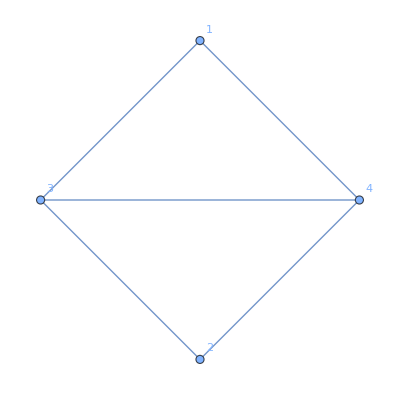

n = 4, GraphIndex = 2, Vertices = {2}

-Graphics-

n = 7, GraphIndex = 638, Vertices = {1}

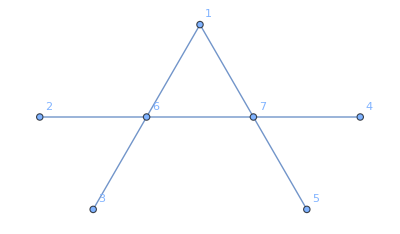

=== Match 2 ===

Reduction matrix:

((2 λ)/(-2+λ^2))

n = 4, GraphIndex = 5, Vertices = {1}

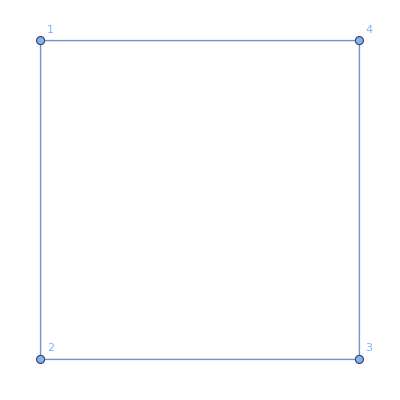

n = 4, GraphIndex = 5, Vertices = {2}

-Graphics-

n = 4, GraphIndex = 5, Vertices = {3}

-Graphics-

n = 4, GraphIndex = 5, Vertices = {4}

-Graphics-

n = 7, GraphIndex = 575, Vertices = {1}

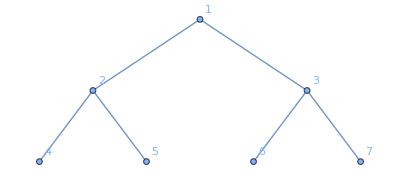

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[2,Length[filteredMatches]]}
]
```

```mathematica
ReductionPowers[n_,m_]:=Module[{graphs},graphs=GraphData/@GraphData["Connected",n];
Flatten[Table[Module[{adjmat,key,powers,numExp,denExp,rpow},adjmat=Simplify[Smash[graphs[[i]],S]];
key=Simplify[Normal[adjmat]];
{powers,numExp,denExp}=Transpose[LeadingPower[#,λ]&/@Flatten[adjmat]];
rpow=ReductionPower[adjmat,λ];
<|"n"->n,"GraphIndex"->i,"Vertices"->S,"Reduction"->key,"ReductionPower"->rpow,"Powers"->powers,"NumExp"->numExp,"DenExp"->denExp|>],{i,Length[graphs]},{S,Subsets[Range[n],{m}]}],1]]

TargetReductionPower[expr_,λ_]:=LeadingPower[expr,λ][[1]]

target=TargetReductionPower[1/λ,λ];

Select[data,#ReductionPower==target&]

FindReductionMatches[data_,expr_,λ_]:=Module[{p=TargetReductionPower[expr,λ]},Select[data,#ReductionPower==p&]]

matches=FindReductionMatches[data,1/λ,λ];
Length[matches]

GroupBy[matches,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&]
```

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==target& cannot be filled from <|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

General::stop: Further output of Function::slota will be suppressed during this calculation.

{}

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

Function::slota: Named slot ReductionPower in #ReductionPower==p$2343759& cannot be filled from <|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>.

General::stop: Further output of Function::slota will be suppressed during this calculation.

0

<||>

## Single Vertex Reduction Examples

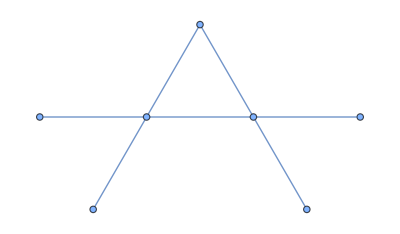

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]]
Simplify[Smash[g,{1}]]
```

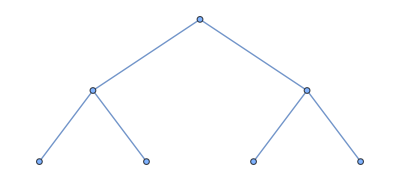

{{λ/(-2+λ^2),1},{1,2/λ}}

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[575]]
Simplify[Smash[g,{1,2}]]
```

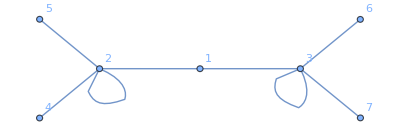

{{-(2 λ)/(2+λ-λ^2)}}

```mathematica
graph=G = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
Simplify[Smash[graph,{1}]]
```

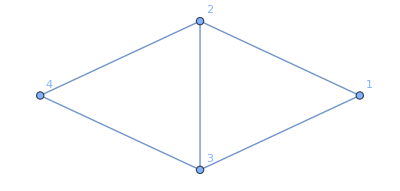

{{λ/(-1+λ^2),λ/(-1+λ)},{λ/(-1+λ),2/(-1+λ)}}

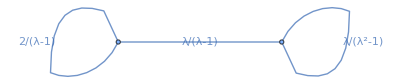

```mathematica
graph=G = Graph[{1<->2,1<->3,2<->3,2<->4,3<->4}, VertexLabels->"Name"]
adjmat=Simplify[Smash[graph,{1,2}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{λ/(-2+λ^2),(-2+λ+λ^2)/(-2+λ^2)},{(-2+λ+λ^2)/(-2+λ^2),(4-3 λ^2)/(2 λ-λ^3)}}

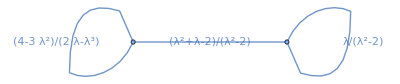

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{1,6}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

## Double Vertex Reduction Matching

```mathematica
data=Flatten@Table[ReductionPowers[n,2],{n,4,8}];
sameReductions=GroupBy[data,Simplify[#Reduction]&,#[[All,{"n","GraphIndex","Vertices"}]]&];
matches=Select[sameReductions,Length[#]>1&];
data // Length (*how many original graphs there are*)
Length[matches]     (*how many unique reductions appear in multiple graphs*)
matches[[1]]
```

40503

8342

{<|n→4,GraphIndex→1,Vertices→{1,2}|>,<|n→4,GraphIndex→1,Vertices→{1,3}|>,<|n→4,GraphIndex→1,Vertices→{2,3}|>}

```mathematica
filteredMatches=Select[
matches,
Module[{group=#,ns,ids},
ns=group[[All,"n"]];
ids=group[[All,"GraphIndex"]];
(Length[DeleteDuplicates[Transpose[{ns,ids}]]]>1)
]&
];
Length[filteredMatches]
```

78

=== Match 1 ===

Reduction matrix:

((2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2)
(2 λ)/(-2+λ^2) | (2 λ)/(-2+λ^2))

n = 5, GraphIndex = 5, Vertices = {3, 4}

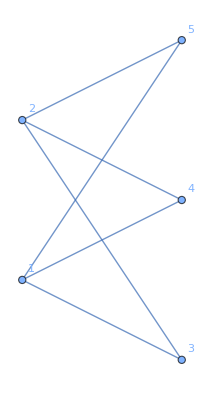

n = 5, GraphIndex = 5, Vertices = {3, 5}

-Graphics-

n = 5, GraphIndex = 5, Vertices = {4, 5}

-Graphics-

n = 8, GraphIndex = 333, Vertices = {2, 3}

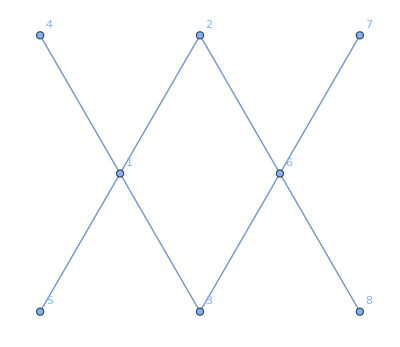

=== Match 2 ===

Reduction matrix:

((-3+2 λ+3 λ^2)/(λ (-2+λ^2)) | (-1+2 λ+2 λ^2)/(λ (-2+λ^2))
(-1+2 λ+2 λ^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 5}

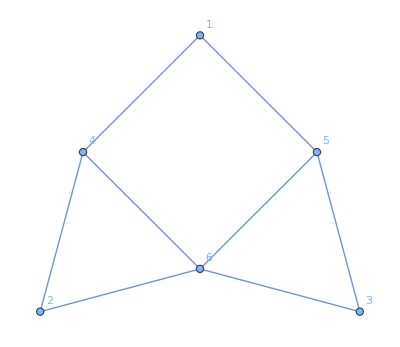

n = 7, GraphIndex = 668, Vertices = {5, 6}

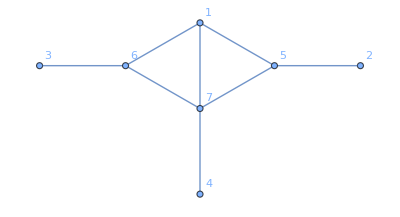

=== Match 3 ===

Reduction matrix:

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

n = 6, GraphIndex = 47, Vertices = {4, 6}

-Graphics-

n = 6, GraphIndex = 47, Vertices = {5, 6}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {5, 7}

-Graphics-

n = 7, GraphIndex = 668, Vertices = {6, 7}

-Graphics-

```mathematica
Do[
Print[
Style["=== Match "<>ToString[i]<>" ===",Bold,Blue]
];
key=Keys[filteredMatches][[i]];(*the shared reduction matrix*)
group=filteredMatches[[i]];(*list of entries with that reduction*)

Print["Reduction matrix:"];
MatrixForm[key]//Print;

(*loop through each graph that gave this reduction*)
Do[
With[{n=assoc["n"],gidx=assoc["GraphIndex"],verts=assoc["Vertices"]},
Print[
Style["n = "<>ToString[n]<>", GraphIndex = "<>ToString[gidx]<>", Vertices = "<>ToString[verts],Darker@Green]
];
graphs=GraphData/@GraphData["Connected",n];
g=graphs[[gidx]];
Print[Graph[g,VertexLabels->"Name"]];
],
{assoc,group}
],
{i,Min[3,Length[filteredMatches]]}
]
```

## Double Vertex Reduction Examples

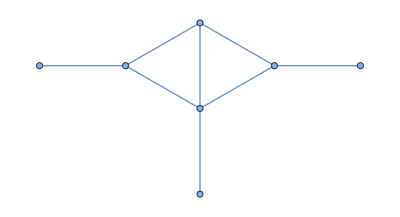

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

((3-2 λ^2)/(2 λ-λ^3) | ((-1+λ) (1+λ)^2)/(λ (-2+λ^2))
((-1+λ) (1+λ)^2)/(λ (-2+λ^2)) | (-3+2 λ+3 λ^2)/(λ (-2+λ^2)))

```mathematica
graphs=GraphData/@GraphData["Connected",7];
g=graphs[[668]]
MatrixForm[Simplify[Smash[g,{5,7}]]]
```

## Automorphism Unfolding

```mathematica
graphs=GraphData/@GraphData["Connected",7];
```

-Graphics-

{{2/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ)},{1/(-1+λ),λ/(-1+λ^2),λ/(-1+λ^2),1/(-1+λ^2),1/(-1+λ^2)},{1/(-1+λ),λ/(-1+λ^2),λ/(-1+λ^2),1/(-1+λ^2),1/(-1+λ^2)},{1/(-1+λ),1/(-1+λ^2),1/(-1+λ^2),λ/(-1+λ^2),λ/(-1+λ^2)},{1/(-1+λ),1/(-1+λ^2),1/(-1+λ^2),λ/(-1+λ^2),λ/(-1+λ^2)}}

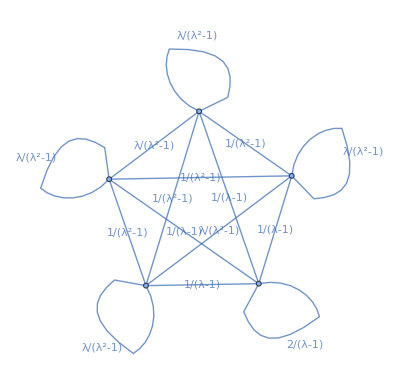

```mathematica
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{1,2,3,4,5}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{2/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ),1/(-1+λ)},{1/(-1+λ),1/(-1+λ),1/(-1+λ),0,0},{1/(-1+λ),1/(-1+λ),1/(-1+λ),0,0},{1/(-1+λ),0,0,1/(-1+λ),1/(-1+λ)},{1/(-1+λ),0,0,1/(-1+λ),1/(-1+λ)}}

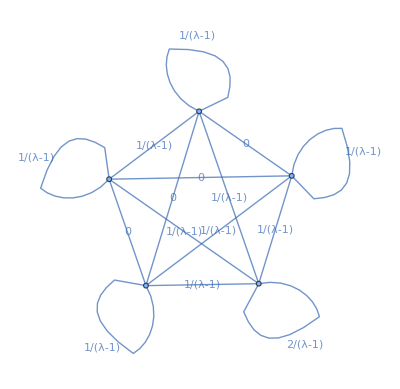

```mathematica
g = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
adjmat=Simplify[Smash[g,{1,4,5,6,7}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),1/(-2-λ+λ^2),1/(-2-λ+λ^2)},{(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),1/(-2-λ+λ^2),1/(-2-λ+λ^2)},{1/(-2-λ+λ^2),1/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2)},{1/(-2-λ+λ^2),1/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2),(-1+λ)/(-2-λ+λ^2)}}

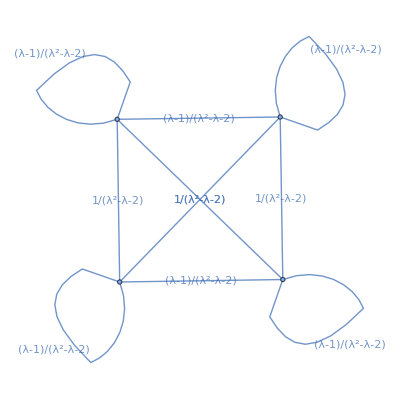

```mathematica
g=graphs[[638]];
Print[Graph[g,VertexLabels->"Name"]];
adjmat=Simplify[Smash[g,{2,3,4,5}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

-Graphics-

{{(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3)},{(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3)},{1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3)},{1/(2-λ-2 λ^2+λ^3),1/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3),(-1-λ+λ^2)/(2-λ-2 λ^2+λ^3)}}

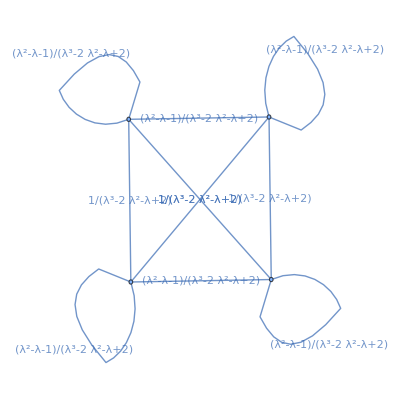

```mathematica
g = Graph[{1<->2, 1<->3,2<->2,2<->4,2<->5,3<->3,3<->6,3<->7}, VertexLabels->"Name"]
adjmat=Simplify[Smash[g,{4,5,6,7}]]
redGraph = WeightedAdjacencyGraph[adjmat];
Graph[redGraph, EdgeLabels->"EdgeWeight"]
```

```mathematica
Factor[x^3-2 x^2-x+2]
Factor[x^2-x-1]
```

(-2+x) (-1+x) (1+x)

-1-x+x^2

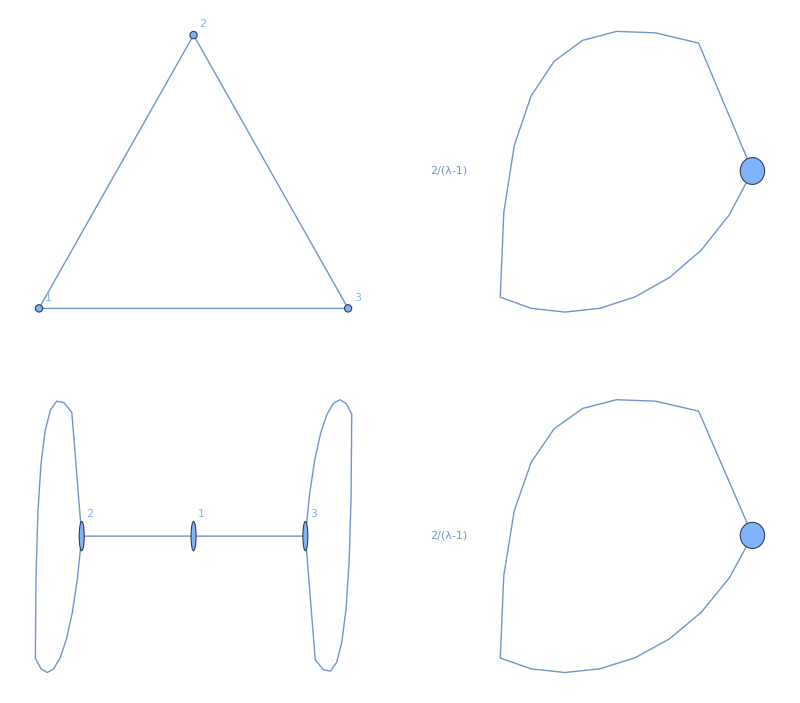

```mathematica
g = Graph[{1<->2, 2<->3,3<->1}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 2<->2,3<->3}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

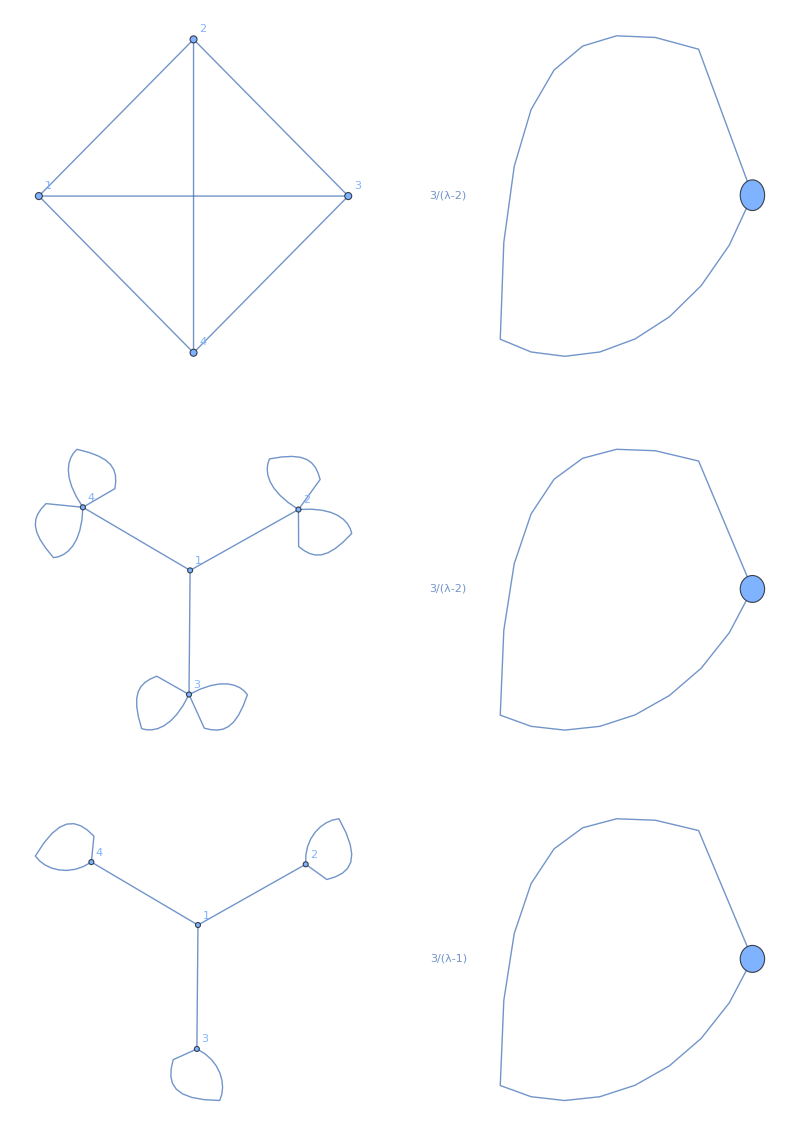

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,2<->3,2<->4,3<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,2<->2,2<->2,3<->3,3<->3,4<->4,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,2<->2,3<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG2, compRedGraph2}
}
]
```

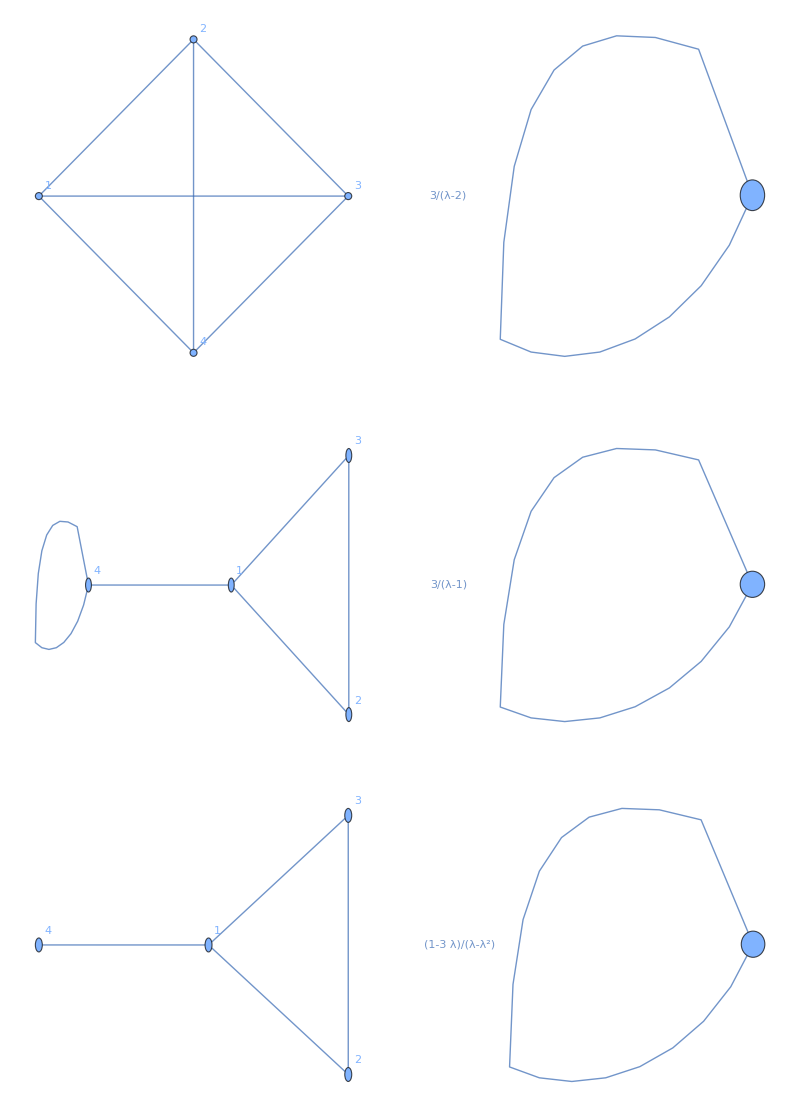

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,2<->3,2<->4,3<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,2<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,2<->3}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG2, compRedGraph2}
}
]
```

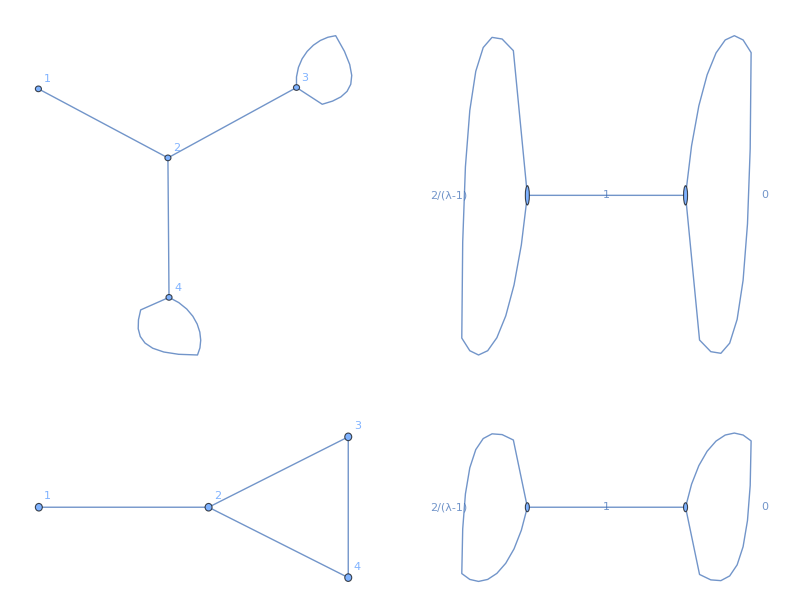

```mathematica
g = Graph[{1<->2,2<->3,2<->4,3<->3,4<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1,2}]];
redGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,2<->3,3<->4,2<->4}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1,2}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

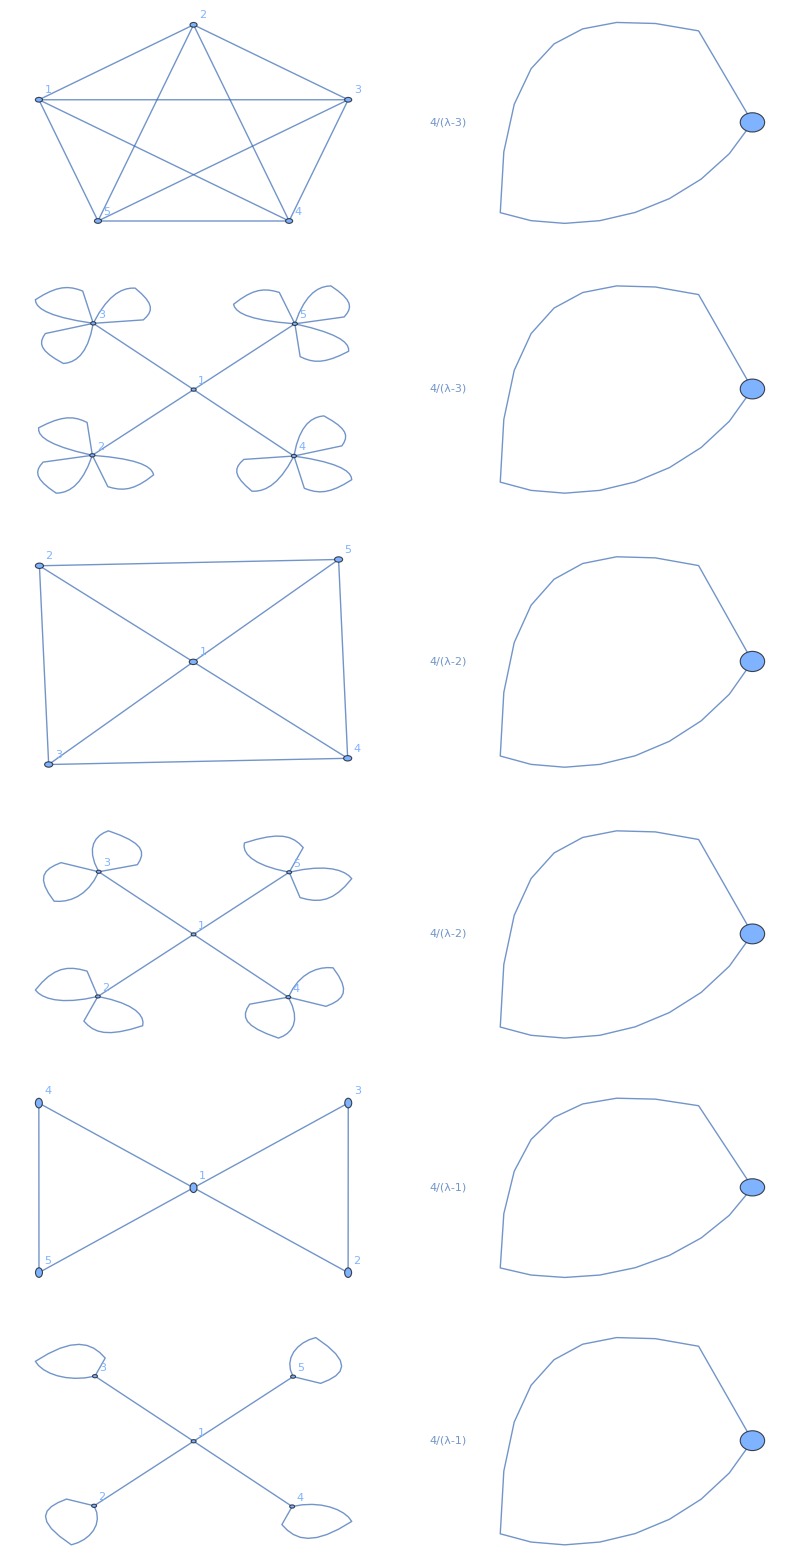

```mathematica
g = Graph[{1<->2, 1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,2<->2,2<->2,3<->3,3<->3,3<->3,4<->4,4<->4,4<->4,5<->5,5<->5,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG1 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->3,3<->4,4<->5,5<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG1,{1}]];
compRedGraph1 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG2 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,2<->2,3<->3,3<->3,4<->4,4<->4,5<->5,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG2,{1}]];
compRedGraph2 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG3 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->3,4<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG3,{1}]];
compRedGraph3 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG4 = Graph[{1<->2,1<->3, 1<->4,1<->5,2<->2,3<->3,4<->4,5<->5}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG4,{1}]];
compRedGraph4 = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];


GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph},
{compG1, compRedGraph1},
{compG2, compRedGraph2},
{compG3, compRedGraph3},
{compG4, compRedGraph4}
}
]
```

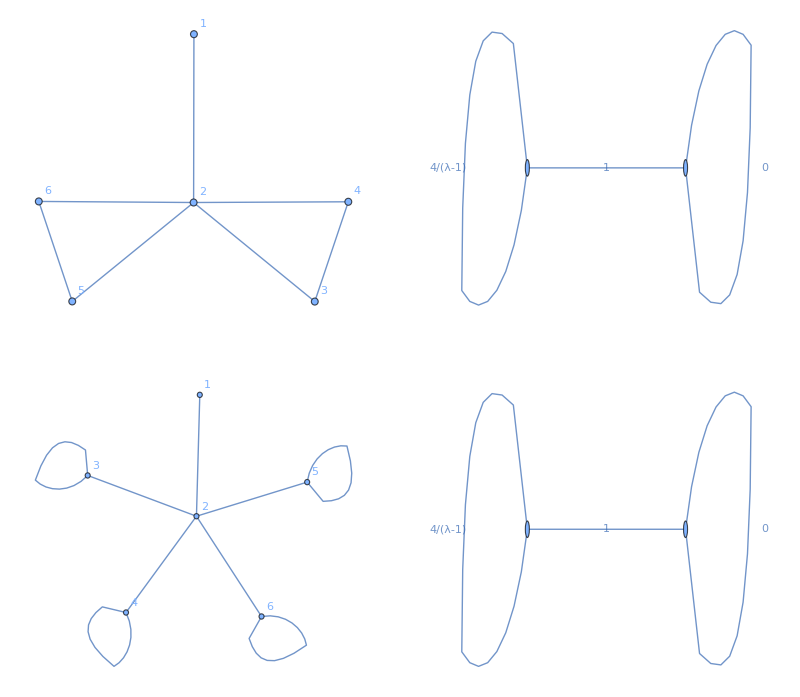

```mathematica
g = Graph[{1<->2,2<->3,3<->4,4<->2,2<->5,5<->6,6<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1,2}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,2<->3,3<->3,4<->4,4<->2,2<->5,5<->5,6<->6,6<->2}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1,2}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

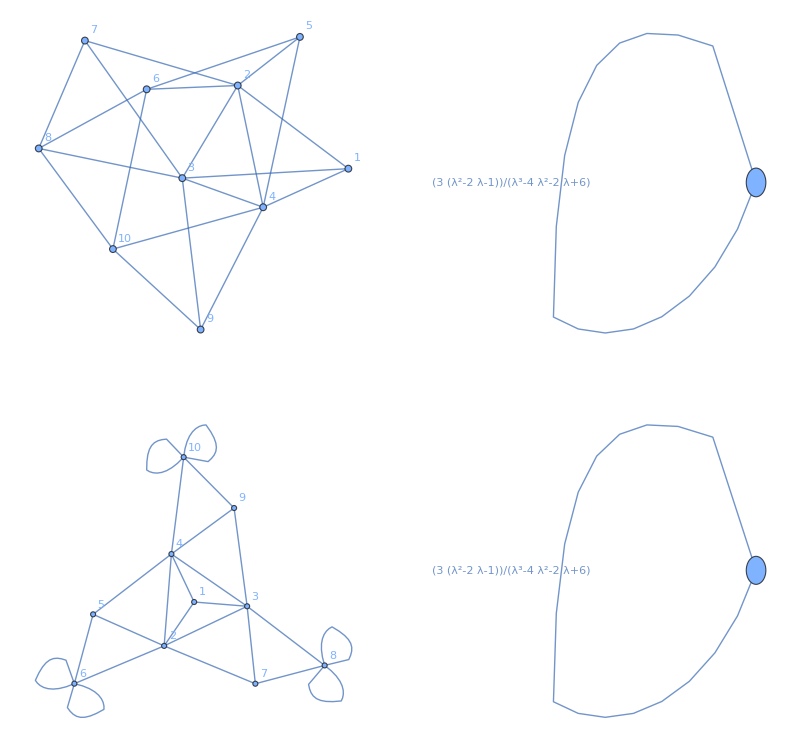

```mathematica
g = Graph[{1<->2,1<->3,1<->4,2<->4,2<->3,3<->4,4<->5,5<->2,2<->6,5<->6,2<->7,3<->7,3<->8,7<->8,4<->9,3<->9,10<->4,10<->9,8<->6,10<->8,10<->6}, VertexLabels->"Name"];
adjmat=Simplify[Smash[g,{1}]];
redGraph =Graph[ WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

compG = Graph[{1<->2,1<->3,1<->4,2<->4,2<->3,3<->4,4<->5,5<->2,2<->6,5<->6,6<->6,2<->7,3<->7,3<->8,7<->8,8<->8,4<->9,3<->9,10<->4,10<->9,10<->10,10<->10,6<->6,8<->8}, VertexLabels->"Name"];
adjmat=Simplify[Smash[compG,{1}]];
compRedGraph = Graph[WeightedAdjacencyGraph[adjmat], EdgeLabels->"EdgeWeight"];

GraphicsGrid[
{
{g,redGraph},
{compG, compRedGraph}
}
]
```

## Single Vertex Reduction Matching Given Examples

```mathematica
data=Flatten@Table[ReductionPowers[n,1],{n,4,12}];
```

```mathematica
target = (λ-1)/λ;
matches = Select[
data,
Simplify[First[Flatten[#Reduction]]==target] &
]
Length[matches]
```

{}

0

```mathematica
graphs=GraphData/@GraphData["Connected",5];
Print[Graph[graphs[[21]],VertexLabels->"Name"]];
```

-Graphics-

```mathematica
matches = Select[
data,
#n==4 &
]
Length[matches]
```

{<|n→4,GraphIndex→1,Vertices→{1},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{2},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{3},Reduction→{{λ/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→1,Vertices→{4},Reduction→{{3/λ}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→2,Vertices→{1},Reduction→{{-(2 λ)/(2+λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{2},Reduction→{{-(2 λ)/(2+λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{3},Reduction→{{(4+3 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→2,Vertices→{4},Reduction→{{(4+3 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→3,Vertices→{1},Reduction→{{(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{2},Reduction→{{(1-2 λ^2)/(λ-λ^3)}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{3},Reduction→{{(1-2 λ^2)/(λ-λ^3)}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→3,Vertices→{4},Reduction→{{(-1+λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{1},Reduction→{{(-1+2 λ+2 λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{2},Reduction→{{(-1+2 λ+2 λ^2)/(λ (-2+λ^2))}},Powers→{-1},NumExp→{2},DenExp→{3}|>,<|n→4,GraphIndex→4,Vertices→{3},Reduction→{{(1-3 λ)/(λ-λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→4,Vertices→{4},Reduction→{{(-1+λ)/(-2-λ+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{1},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{2},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{3},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→5,Vertices→{4},Reduction→{{(2 λ)/(-2+λ^2)}},Powers→{-1},NumExp→{1},DenExp→{2}|>,<|n→4,GraphIndex→6,Vertices→{1},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{2},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{3},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>,<|n→4,GraphIndex→6,Vertices→{4},Reduction→{{3/(-2+λ)}},Powers→{-1},NumExp→{0},DenExp→{1}|>}

24

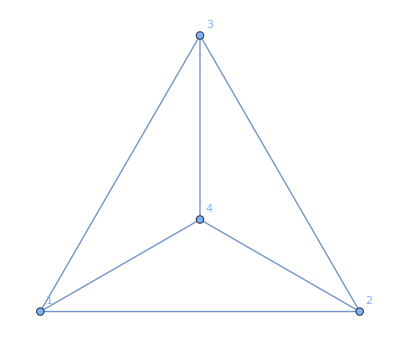

```mathematica
graphs=GraphData/@GraphData["Connected",4];
Print[Graph[graphs[[6]],VertexLabels->"Name"]];
```

## Automorphism Proof Work

```mathematica
g=Graph[{1<->2,2<->3,3<->5,5<->4,4<->1},VertexLabels->"Name"];
g1 = Graph[{1<->2,2<->3,3<->5,5<->4,4<->1,2<->2,4<->4},VertexLabels->"Name"];
g2 = Graph[{1<->2,2<->3,3<->5,5<->4,4<->1,2<->4},VertexLabels->"Name"];

GraphicsRow[{
Labeled[g,"g",Top],
Labeled[g1,"g1",Top],
Labeled[g2,"g2",Top]
}]
```

-Graphics-

```mathematica
g1A = {{0,1,0,1,0},{1,1,1,0,0},{0,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0}}
g2A = {{0,1,0,1,0},{1,0,1,1,0},{0,1,0,0,1},{1,1,0,0,1},{0,0,1,1,0}}

split=1; (*Vertex to split on*)

g1m11=g1A[[1;;split,1;;split]]
g1m12=g1A[[1;;split,split+1;;]]
g1m21=g1A[[split+1;;,1;;split]]
g1m22=g1A[[split+1;;,split+1;;]]
s = Length[m22]

Simplify[g1m11 + g1m12.Inverse[λ IdentityMatrix[s] - g1m22].g1m21]

g2m11=g2A[[1;;split,1;;split]]
g2m12=g2A[[1;;split,split+1;;]]
g2m21=g2A[[split+1;;,1;;split]]
g2m22=g2A[[split+1;;,split+1;;]]
s = Length[m22]

Simplify[g2m11 +g2m12.Inverse[λ IdentityMatrix[s] - g2m22].g2m21]
```

{{0,1,0,1,0},{1,1,1,0,0},{0,1,0,0,1},{1,0,0,1,1},{0,0,1,1,0}}

{{0,1,0,1,0},{1,0,1,1,0},{0,1,0,0,1},{1,1,0,0,1},{0,0,1,1,0}}

{{0}}

{{1,0,1,0}}

{{1},{0},{1},{0}}

{{1,1,0,0},{1,0,0,1},{0,0,1,1},{0,1,1,0}}

4

{{(2 (-1+λ))/((-2+λ) λ)}}

{{0}}

{{1,0,1,0}}

{{1},{0},{1},{0}}

{{0,1,1,0},{1,0,0,1},{1,0,0,1},{0,1,1,0}}

4

{{(2 (-1+λ))/((-2+λ) λ)}}

```mathematica
Row[{MatrixForm[g1m22],Spacer[20],MatrixForm[g2m22]}]
Row[{MatrixForm[λ IdentityMatrix[s] - g1m22],Spacer[20],MatrixForm[λ IdentityMatrix[s] - g2m22]}]
g1mInv = Simplify[Inverse[λ IdentityMatrix[s] - g1m22]];
g2mInv = Simplify[Inverse[λ IdentityMatrix[s] - g2m22]];
Row[{MatrixForm[g1mInv],Spacer[20],MatrixForm[g2mInv]}]

g1m12
g2m12
Simplify[g1m12.g1mInv]
Simplify[g2m12.g2mInv]

g1m21
g2m21
Simplify[g1mInv.g1m21]
Simplify[g2mInv.g1m21]
```

(1 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 1 | 0)(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

(-1+λ | -1 | 0 | 0
-1 | λ | 0 | -1
0 | 0 | -1+λ | -1
0 | -1 | -1 | λ)(λ | -1 | -1 | 0
-1 | λ | 0 | -1
-1 | 0 | λ | -1
0 | -1 | -1 | λ)

((1-2 λ-λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | 1/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3))
(-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (-1+λ)^2/(λ (4-2 λ-2 λ^2+λ^3))
1/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ-λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3))
(-1+λ)/(λ (4-2 λ-2 λ^2+λ^3)) | (-1+λ)^2/(λ (4-2 λ-2 λ^2+λ^3)) | (-1-λ+λ^2)/(λ (4-2 λ-2 λ^2+λ^3)) | (1-2 λ^2+λ^3)/(4 λ-2 λ^2-2 λ^3+λ^4))((-2+λ^2)/(-4 λ+λ^3) | 1/(-4+λ^2) | 1/(-4+λ^2) | 2/(-4 λ+λ^3)
1/(-4+λ^2) | (-2+λ^2)/(-4 λ+λ^3) | 2/(-4 λ+λ^3) | 1/(-4+λ^2)
1/(-4+λ^2) | 2/(-4 λ+λ^3) | (-2+λ^2)/(-4 λ+λ^3) | 1/(-4+λ^2)
2/(-4 λ+λ^3) | 1/(-4+λ^2) | 1/(-4+λ^2) | (-2+λ^2)/(-4 λ+λ^3))

{{1,0,1,0}}

{{1,0,1,0}}

{{(-1+λ)/((-2+λ) λ),1/((-2+λ) λ),(-1+λ)/((-2+λ) λ),1/((-2+λ) λ)}}

{{(-1+λ)/((-2+λ) λ),1/((-2+λ) λ),(-1+λ)/((-2+λ) λ),1/((-2+λ) λ)}}

{{1},{0},{1},{0}}

{{1},{0},{1},{0}}

{{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)},{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)}}

{{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)},{(-1+λ)/((-2+λ) λ)},{1/((-2+λ) λ)}}

```mathematica
P={{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,1,0,0}}
MatrixForm[P]
MatrixForm[Transpose[P].g1A.P]==MatrixForm[g1A]
Row[{MatrixForm[g1A],Spacer[20],MatrixForm[g2A]}]
Row[{MatrixForm[g1A[[2;;,2;;]]],Spacer[20],MatrixForm[g2A[[2;;,2;;]]]}]
Row[{MatrixForm[(g2A.P)[[2;;,2;;]]],Spacer[20],MatrixForm[(g1A.P)[[2;;,2;;]]]}]
```

{{1,0,0,0,0},{0,0,0,1,0},{0,0,0,0,1},{0,1,0,0,0},{0,0,1,0,0}}

(1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0)

True

(0 | 1 | 0 | 1 | 0
1 | 1 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 0)(0 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0
0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 0)

(1 | 1 | 0 | 0
1 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 1 | 1 | 0)(0 | 1 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 0)

(1 | 0 | 0 | 1
0 | 1 | 1 | 0
0 | 1 | 1 | 0
1 | 0 | 0 | 1)(0 | 0 | 1 | 1
0 | 1 | 1 | 0
1 | 1 | 0 | 0
1 | 0 | 0 | 1)

```mathematica
i=3;
Row[{MatrixForm[g1m12],Spacer[20],MatrixForm[g2m12]}]
Row[{MatrixForm[MatrixPower[g1m22,i]],Spacer[20],MatrixForm[MatrixPower[g2m22,i]]}]
Row[{MatrixForm[g1m12.MatrixPower[g1m22,i]],MatrixForm[g2m12.MatrixPower[g2m22,i]]}]
Row[{MatrixForm[g1m12.MatrixPower[g1m22,i].g1m21],MatrixForm[g2m12.MatrixPower[g2m22,i].g2m21]}]
```

(1 | 0 | 1 | 0)(1 | 0 | 1 | 0)

(3 | 3 | 1 | 1
3 | 1 | 1 | 3
1 | 1 | 3 | 3
1 | 3 | 3 | 1)(0 | 4 | 4 | 0
4 | 0 | 0 | 4
4 | 0 | 0 | 4
0 | 4 | 4 | 0)

(4 | 4 | 4 | 4)(4 | 4 | 4 | 4)

(8)(8)

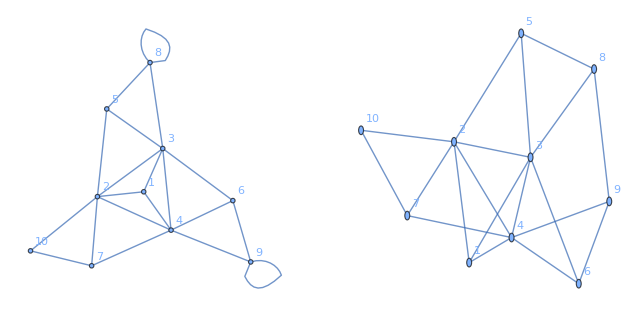

```mathematica
t1A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,1,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,0}
};
t2A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,1,0},
{0,0,0,1,0,1,0,1,0,0},
{0,1,0,0,0,0,1,0,0,0}
};
GraphicsRow[{AdjacencyGraph[t1A,VertexLabels->Automatic],AdjacencyGraph[t2A,VertexLabels->Automatic]}]
```

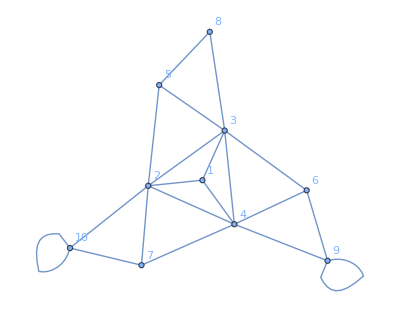

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(-15+8 λ-37 λ^3+18 λ^4-7 λ^5+12 λ^6-6 λ^7+3 λ^8)/(6-26 λ+24 λ^2-22 λ^3-25 λ^4-8 λ^5-5 λ^6+3 λ^7-4 λ^8+λ^9)}}

{{(-5+11 λ-25 λ^2-36 λ^3+32 λ^4-10 λ^5+9 λ^6-3 λ^7+3 λ^8)/(2-12 λ+24 λ^2-50 λ^3-32 λ^4-λ^5-9 λ^6-3 λ^8+λ^9)}}

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
AdjacencyGraph[Transpose[P].t1A.P,VertexLabels->Automatic]

Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
Simplify[t1m11 + t1m12.Inverse[λ IdentityMatrix[s] - t1m22].t1m21]

split=1; (*Vertex to split on*)

t1m11P=(t1A.Transpose[P])[[1;;split,1;;split]];
t1m12P=(t1A.Transpose[P])[[1;;split,split+1;;]];
t1m21P=(t1A.Transpose[P])[[split+1;;,1;;split]];
t1m22P=(t1A.Transpose[P])[[split+1;;,split+1;;]];
s = Length[t1m22];

t2m11P=(t2A.Transpose[P])[[1;;split,1;;split]];
t2m12P=(t2A.Transpose[P])[[1;;split,split+1;;]];
t2m21=(t2A.Transpose[P])[[split+1;;,1;;split]];
t2m22P=(t2A.Transpose[P])[[split+1;;,split+1;;]];
s = Length[t2m22];

Simplify[t2m11P +t2m12P.Inverse[λ IdentityMatrix[s] - t2m22P].t2m21]
Simplify[t1m11P + t1m12P.Inverse[λ IdentityMatrix[s] - t1m22P].t1m21]
```

```mathematica
i=1;
Row[{MatrixForm[t1m12],Spacer[20],MatrixForm[t2m12]}]
Row[{MatrixForm[MatrixPower[t1m22,i]],Spacer[20],MatrixForm[MatrixPower[t2m22,i]]}]
Row[{MatrixForm[t1m12.MatrixPower[t1m22,i]],MatrixForm[t2m12.MatrixPower[t2m22,i]]}]
Row[{MatrixForm[t1m12.MatrixPower[t1m22,i].t1m21],MatrixForm[t2m12.MatrixPower[t2m22,i].t2m21]}]
```

(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)(1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1)(2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 1)

(6)(6)

```mathematica
MatrixForm[Transpose[P].Transpose[P].Transpose[P].t1A.P.P.P]==MatrixForm[t1A]
Row[{MatrixForm[t1A],Spacer[20],MatrixForm[t2A]}]
Row[{MatrixForm[t1A[[2;;,2;;]]],Spacer[20],MatrixForm[t2A[[2;;,2;;]]]}]
Row[{MatrixForm[(t2A.P)[[2;;,2;;]]],Spacer[20],MatrixForm[(t1A.P)[[2;;,2;;]]]}]



Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
Simplify[t2m11 +t2m12.Inverse[λ IdentityMatrix[s] - t2m22].t2m21]
```

True

(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

(1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0)(1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0)

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

```mathematica
M={{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}
{U,V}=ResourceFunction["FullRankDecomposition"][M]
M==U.V
Row[{MatrixForm[U], MatrixForm[V]}]
```

{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}

{{{0,0},{1,0},{0,1},{0,0}},{{0,1,0,0},{0,0,1,0}}}

True

(0 | 0
1 | 0
0 | 1
0 | 0)(0 | 1 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
M={{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}
{U,V}=ResourceFunction["FullRankDecomposition"][M]
M==U.V
Row[{MatrixForm[U], MatrixForm[V]}]
```

{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}

{{{0,0},{0,1},{1,0},{0,0}},{{0,1,0,0},{0,0,1,0}}}

True

(0 | 0
0 | 1
1 | 0
0 | 0)(0 | 1 | 0 | 0
0 | 0 | 1 | 0)

### Eigensystem of M_(Sbar,Sbar)

```mathematica
Mat1={{-l,0,1,0},{0,-l,0,1},{1,0,1-l,0},{0,1,0,1-l}}
Mat1Inv=Inverse[Mat1]

Mat2={{-l,0,1,0},{0,-l,0,1},{1,0,-l,1},{0,1,1,-l}}
Mat2Inv=Inverse[Mat2]

Simplify[{{1,1,0,0}}.Mat1Inv]
Simplify[{{1,1,0,0}}.Mat2Inv]
```

{{-l,0,1,0},{0,-l,0,1},{1,0,1-l,0},{0,1,0,1-l}}

{{(1-l)/(-1-l+l^2),0,-1/(-1-l+l^2),0},{0,(1-l)/(-1-l+l^2),0,-1/(-1-l+l^2)},{-1/(-1-l+l^2),0,-l/(-1-l+l^2),0},{0,-1/(-1-l+l^2),0,-l/(-1-l+l^2)}}

{{-l,0,1,0},{0,-l,0,1},{1,0,-l,1},{0,1,1,-l}}

{{(2 l-l^3)/(1-3 l^2+l^4),-1/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4)},{-1/(1-3 l^2+l^4),(2 l-l^3)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4)},{(1-l^2)/(1-3 l^2+l^4),-l/(1-3 l^2+l^4),(l-l^3)/(1-3 l^2+l^4),-l^2/(1-3 l^2+l^4)},{-l/(1-3 l^2+l^4),(1-l^2)/(1-3 l^2+l^4),-l^2/(1-3 l^2+l^4),(l-l^3)/(1-3 l^2+l^4)}}

{{(1-l)/(-1-l+l^2),(1-l)/(-1-l+l^2),1/(1+l-l^2),1/(1+l-l^2)}}

{{(1-l)/(-1-l+l^2),(1-l)/(-1-l+l^2),1/(1+l-l^2),1/(1+l-l^2)}}

(0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

{{2,2,1},{2,2,1},{2,2,1},{2,0,1},{2,0,1},{2,0,1},{1,1,0},{1,1,0},{1,1,0}}

{,,,,,,1,1,1}

{,,,,,,1,1,1}

{,-2,-2,1/2 (1+√5),1/2 (1+√5),,1/2 (1-√5),1/2 (1-√5),}

{,,}

{{2,2,1},{2,2,1},{2,2,1},{2,0,1},{2,0,1},{2,0,1},{1,1,0},{1,1,0},{1,1,0}}

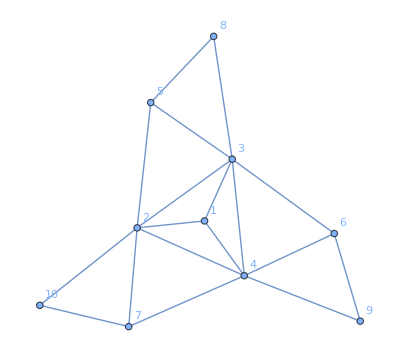

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
A = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,0},
{0,1,0,0,0,0,1,0,0,0}
};
autA = A[[2;;,2;;]];
MatrixForm[autA]
S={{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1}};
B={{2,2,1},{2,0,1},{1,1,0}};
S.B
S.Eigenvectors[B][[1]]
Eigenvectors[autA][[1]]
Eigenvalues[autA]
Eigenvalues[B]
autA.S
AdjacencyGraph[A,VertexLabels->Automatic]
```

{{,,,,,,,,1,1},{0,,,,,,,0,-1,1},{,,,,,,,,1,1},{0,,,,,,,0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{0,,,,,,,0,-1,1}}

{{,,,,,,,,1,1},{0,-(23-5 √13)/(2 (-7+3 √13)),-1/2,-(-8+√13)/(-7+3 √13),-(2 (-89+26 √13))/((-7+3 √13) (-23+5 √13)),-(-15+4 √13)/(-7+3 √13),-(23-5 √13)/(2 (-7+3 √13)),0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{0,-(-23-5 √13)/(2 (7+3 √13)),-1/2,-(8+√13)/(7+3 √13),(2 (89+26 √13))/((7+3 √13) (23+5 √13)),-(15+4 √13)/(7+3 √13),-(-23-5 √13)/(2 (7+3 √13)),0,-1,1},{0,0,1,-1,-1,1,0,0,-1,1},{,,,,,,,,1,1},{,,,,,,,,1,1},{,,,,,,,,1,1}}

{,,,,,,,,}

{,1/2 (-1-√13),,,,1/2 (-1+√13),-1,,}

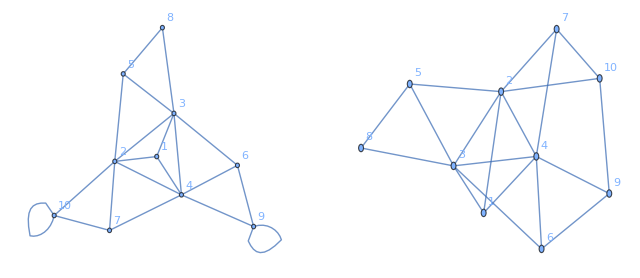

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{{(5+14 λ-λ^2-15 λ^3+3 λ^5)/(-2+6 λ+22 λ^2+5 λ^3-10 λ^4-2 λ^5+λ^6)}}

{,,,,,,,,,}

{,1/2 (-1-√13),,,,1/2 (-1+√13),-1,,,}

{{λ→},{λ→},{λ→},{λ→},{λ→},{λ→},{λ→}}

{{λ→},{λ→},{λ→},{λ→},{λ→},{λ→},{λ→}}

```mathematica
P={
{1,0,0,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0,0},
{0,1,0,0,0,0,0,0,0,0},
{0,0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,0,1,0,0,0},
{0,0,0,0,1,0,0,0,0,0},
{0,0,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,0,1},
{0,0,0,0,0,0,0,1,0,0}
};
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,1},
{0,1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[autA1]
Eigenvalues[autA2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Eigenvalues[A1]
Eigenvalues[A2]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

```mathematica
autAL = autA - λ IdentityMatrix[Length[autA]];
MatrixForm[autAL]
S={{1,0,0},{1,0,0},{1,0,0},{0,1,0},{0,1,0},{0,1,0},{0,0,1},{0,0,1},{0,0,1}};
B={{2-λ,2,1},{2,-λ,1},{1,1,-λ}};
S.Eigenvectors[B][[1]]
Eigenvectors[autAL][[1]]
Eigenvalues[autAL][[1]]
S.B
autAL.S
AdjacencyGraph[A,VertexLabels->Automatic]
```

(-λ | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
1 | -λ | 1 | 1 | 1 | 0 | 1 | 0 | 0
1 | 1 | -λ | 0 | 1 | 1 | 0 | 1 | 0
1 | 1 | 0 | -λ | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | -λ | 0 | 0 | 1 | 0
1 | 0 | 1 | 0 | 0 | -λ | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 0 | -λ | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | -λ | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -λ)

{-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(-1-2 λ-2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1])/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),-(1+2 λ-λ^2+2 Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-2 λ Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]-Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]^2)/(λ+Root[-2-6 λ-2 λ^2+λ^3+(-6-4 λ+3 λ^2) #1+(-2+3 λ) #1^2+#1^3&,1]),1,1,1}

{1/2,-(-11+5 √5)/(2 (-7+3 √5)),-(2-√5)/(-7+3 √5),1/4 (-1+√5),-(-2+√5)/(-7+3 √5),-(15-7 √5)/(2 (-7+3 √5)),-1,0,1}

1/2 (1-√5-2 λ)

{{2-λ,2,1},{2-λ,2,1},{2-λ,2,1},{2,-λ,1},{2,-λ,1},{2,-λ,1},{1,1,-λ},{1,1,-λ},{1,1,-λ}}

{{2-λ,2,1},{2-λ,2,1},{2-λ,2,1},{2,-λ,1},{2,-λ,1},{2,-λ,1},{1,1,-λ},{1,1,-λ},{1,1,-λ}}

-Graphics-

{{1,1,1,1,1},{1/2 (1+√5),-1,1/2 (-1-√5),0,1},{1/2 (1+√5),1/2 (-1-√5),-1,1,0},{1/2 (1-√5),-1,1/2 (-1+√5),0,1},{1/2 (1-√5),1/2 (-1+√5),-1,1,0}}

{{1,1,1,1,1},{1+√5,1/2 (-3-√5),1/2 (-3-√5),1,1},{0,1/2 (1-√5),1/2 (-1+√5),-1,1},{0,1/2 (1+√5),1/2 (-1-√5),-1,1},{1-√5,1/2 (-3+√5),1/2 (-3+√5),1,1}}

{2,1/2 (-1-√5),1/2 (-1-√5),1/2 (-1+√5),1/2 (-1+√5)}

{2,1/2 (-1-√5),1/2 (1+√5),1/2 (1-√5),1/2 (-1+√5)}

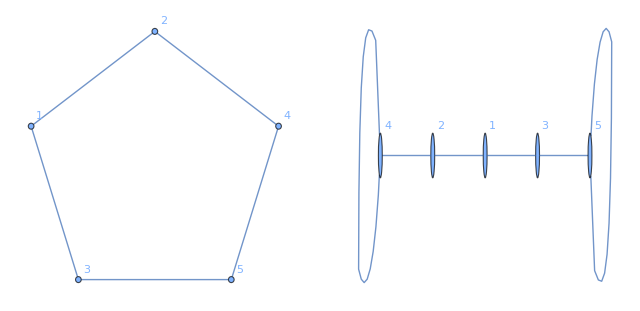

{{(2-2 λ)/(1+λ-λ^2)}}

{{(2-2 λ)/(1+λ-λ^2)}}

{{λ→2},{λ→1/2 (-1-√5)},{λ→1/2 (-1+√5)}}

{{λ→2},{λ→1/2 (-1-√5)},{λ→1/2 (-1+√5)}}

```mathematica
A1 = {
{0,1,1,0,0},
{1,0,0,1,0},
{1,0,0,0,1},
{0,1,0,0,1},
{0,0,1,1,0}
};
A2 = {
{0,1,1,0,0},
{1,0,0,1,0},
{1,0,0,0,1},
{0,1,0,1,0},
{0,0,1,0,1}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{1,1,1,1,1,1,1},{,,,,,1,1},{0,,,,,-1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{{1,1,1,1,1,1,1},{,,,-1,,0,1},{,,,,-1,1,0},{,,,-1,,0,1},{,,,,-1,1,0},{,,,-1,,0,1},{,,,,-1,1,0}}

{2,,,,,,}

{2,,,,,,}

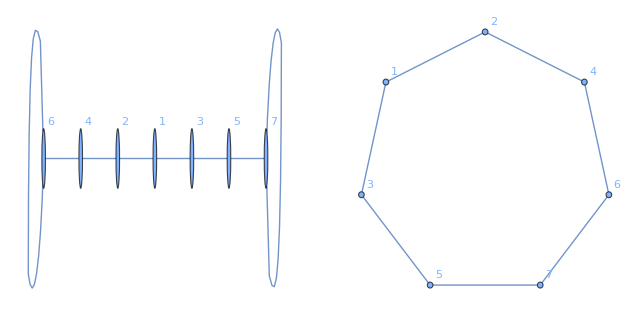

{{(2 (-1-λ+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{(2 (-1-λ+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{λ→2},{λ→},{λ→},{λ→}}

{{λ→2},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,1,0},
{0,0,0,0,1,0,1}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,1},
{0,0,0,0,1,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,,,,1,1},{0,-1,1,2,-2,-1,1},{,,,,,1,1},{-1,-1,0,0,1,0,1},{-1,0,-1,1,0,1,0},{,,,,,1,1},{0,1,-1,0,0,-1,1}}

{{,,,,,1,1},{0,-1,1,-2,2,-1,1},{,,,,,1,1},{0,-1,1,1,-1,-1,1},{-2,-1,-1,1,1,1,1},{,,,,,1,1},{0,1,-1,0,0,-1,1}}

{,-2,,1,1,,0}

{,2,,-1,1,,0}

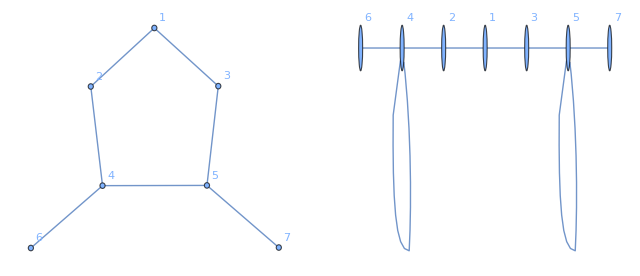

{{(2+2 λ-2 λ^2)/(2 λ+λ^2-λ^3)}}

{{(2+2 λ-2 λ^2)/(2 λ+λ^2-λ^3)}}

{{λ→1},{λ→},{λ→},{λ→}}

{{λ→1},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,0,1,1,0},
{0,0,1,1,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,0,1,0,0,0},
{1,0,0,0,1,0,0},
{0,1,0,1,0,1,0},
{0,0,1,0,1,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

```mathematica
A1 = {
{0,1,1,0,0,0,0},
{1,1,0,1,0,0,0},
{1,0,1,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
A2 = {
{0,1,1,0,0,0,0},
{1,0,1,1,0,0,0},
{1,1,0,0,1,0,0},
{0,1,0,0,0,1,0},
{0,0,1,0,0,0,1},
{0,0,0,1,0,0,0},
{0,0,0,0,1,0,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{0,,,,,-1,1},{,,,,,1,1},{,,,,,1,1},{0,,,,,-1,1}}

{,,,,,,}

{,,,,,,}

-Graphics-

{{(2 (-1+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{(2 (-1+λ^2))/(1-2 λ-λ^2+λ^3)}}

{{λ→},{λ→},{λ→},{λ→}}

{{λ→},{λ→},{λ→},{λ→}}

{{1,1,1,1,1,1,1,1,1},{,,,,,-1,,0,1},{,,,,,,-1,1,0},{,,,,,-1,,0,1},{,,,,,,-1,1,0},{-1,0,1,1,0,-1,-1,0,1},{-1,1,0,0,1,-1,-1,1,0},{,,,,,-1,,0,1},{,,,,,,-1,1,0}}

{{1,1,1,1,1,1,1,1,1},{,,,,,,,1,1},{0,,,,,,,-1,1},{0,,,,,,,-1,1},{,,,,,,,1,1},{-2,1,1,1,1,-2,-2,1,1},{0,1,-1,1,-1,0,0,-1,1},{0,,,,,,,-1,1},{,,,,,,,1,1}}

{2,,,,,-1,-1,,}

{2,,,,,-1,1,,}

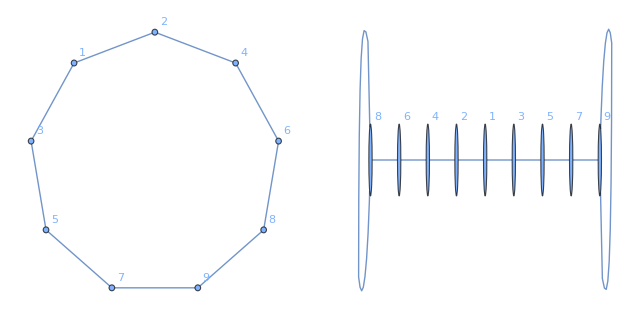

{{(2 (1-2 λ-λ^2+λ^3))/(1+2 λ-3 λ^2-λ^3+λ^4)}}

{{(2 (1-2 λ-λ^2+λ^3))/(1+2 λ-3 λ^2-λ^3+λ^4)}}

{{λ→-1},{λ→2},{λ→},{λ→},{λ→}}

{{λ→-1},{λ→2},{λ→},{λ→},{λ→}}

```mathematica
A1 = {
{0,1,1,0,0,0,0,0,0},
{1,0,0,1,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0},
{0,1,0,0,0,1,0,0,0},
{0,0,1,0,0,0,1,0,0},
{0,0,0,1,0,0,0,1,0},
{0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,1,0,0,1},
{0,0,0,0,0,0,1,1,0}
};
A2 = {
{0,1,1,0,0,0,0,0,0},
{1,0,0,1,0,0,0,0,0},
{1,0,0,0,1,0,0,0,0},
{0,1,0,0,0,1,0,0,0},
{0,0,1,0,0,0,1,0,0},
{0,0,0,1,0,0,0,1,0},
{0,0,0,0,1,0,0,0,1},
{0,0,0,0,0,1,0,1,0},
{0,0,0,0,0,0,1,0,1}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]==0,λ]
```

{{,,1,1},{,,1,1},{0,0,-1,1},{,,1,1}}

{{,,1,1},{,,1,1},{0,0,-1,1},{,,1,1}}

{,,1,}

{,,-1,}

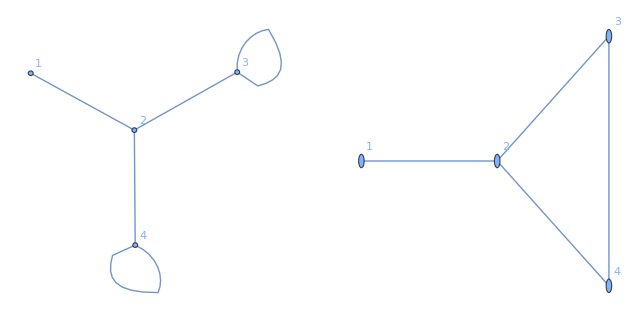

{{0,1},{1,2/(-1+λ)}}

{{0,1},{1,2/(-1+λ)}}

{}

{}

```mathematica
A1 = {
{0,1,0,0},
{1,0,1,1},
{0,1,1,0},
{0,1,0,1}
};
A2 = {
{0,1,0,0},
{1,0,1,1},
{0,1,0,1},
{0,1,1,0}
};
autA1 = A1[[3;;,3;;]];
autA2 = A2[[3;;,3;;]];
Eigenvectors[A1]
Eigenvectors[A2]
Eigenvalues[A1]
Eigenvalues[A2]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1,2}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1,2}]]
Solve[λ-Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1,2}]]==0,λ]
Solve[λ-Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1,2}]]==0,λ]
```

(1 | 1 | 0 | 0
0 | 1 | 1 | 0
1 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0)

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1)(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0)

(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
0 | 1 | 2 | 0
2 | 0 | 1 | 0)(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
1 | 1 | 1 | 0
1 | 0 | 2 | 0)

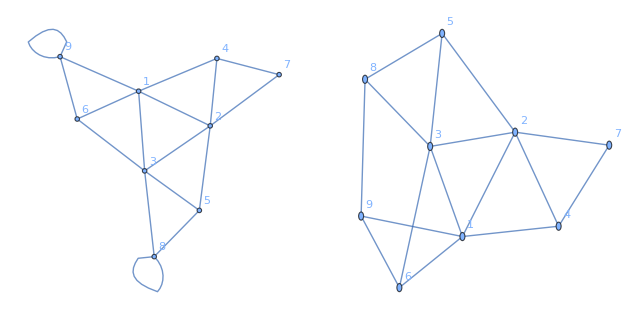

```mathematica
A1 = {
{0,1,1,1,0,1,0,0,1},
{1,0,1,1,1,0,1,0,0},
{1,1,0,0,1,1,0,1,0},
{1,1,0,0,0,0,1,0,0},
{0,1,1,0,0,0,0,1,0},
{1,0,1,0,0,0,0,0,1},
{0,1,0,1,0,0,0,0,0},
{0,0,1,0,1,0,0,1,0},
{1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,1,0,0,1},
{1,0,1,1,1,0,1,0,0},
{1,1,0,0,1,1,0,1,0},
{1,1,0,0,0,0,1,0,0},
{0,1,1,0,0,0,0,1,0},
{1,0,1,0,0,0,0,0,1},
{0,1,0,1,0,0,0,0,0},
{0,0,1,0,1,0,0,0,1},
{1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[4;;,4;;]];
autA2 = A2[[4;;,4;;]];
Mss = A1[[4;;,;;4]];
MatrixForm[Mss]
Row[{MatrixForm[autA1],MatrixForm[autA2]}]
Row[{MatrixForm[autA1.Mss],MatrixForm[autA2.Mss]}]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
```

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0,0,0},
{0,0,0,1,0,1,0,0,0,1},
{0,1,0,0,0,0,1,0,1,0}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=4
Row[{MatrixForm[MatrixPower[autA1,i].Mss],MatrixForm[MatrixPower[autA2,i].Mss]}]
GraphicsRow[{AdjacencyGraph[A1,VertexLabels->Automatic],AdjacencyGraph[A2,VertexLabels->Automatic]}]
```

(1
1
1
0
0
0
0
0
0)

4

(129
125
130
79
84
85
54
75
75)(129
125
130
79
84
85
54
75
75)

-Graphics-

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,1,0,0},
{0,0,0,1,0,1,0,0,1,0},
{0,1,0,0,0,0,1,0,0,1}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,0.5,0.5,0},
{0,0,0,1,0,1,0,0,0.5,0.5},
{0,1,0,0,0,0,1,0,0.5,0.5}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=4
Row[{MatrixForm[MatrixPower[autA1,i].Mss],MatrixForm[MatrixPower[autA2,i].Mss]}]
Row[{Simplify[Smash[WeightedAdjacencyGraph[A1],{1}]], Simplify[Smash[WeightedAdjacencyGraph[A2],{1}]]}]
```

(1
1
1
0
0
0
0
0
0)

4

(131
131
131
85
85
85
75
75
75)(131.
131.
131.
85.
85.
85.
75.
75.
75.)

{{λ/(-9+λ)}}{{λ/(-9+λ)}}

```mathematica
A1 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,2 λ/(λ^2-1),0,0},
{0,0,0,1,0,1,0,0,2 λ/(λ^2-1),0},
{0,1,0,0,0,0,1,0,0,2 λ/(λ^2-1)}
};
A2 = {
{0,1,1,1,0,0,0,0,0,0},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{0,0,1,0,1,0,0,λ/(λ^2-1),λ/(λ^2-1),0},
{0,0,0,1,0,1,0,0,λ/(λ^2-1),λ/(λ^2-1)},
{0,1,0,0,0,0,1,0,λ/(λ^2-1),λ/(λ^2-1)}
};
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A1[[2;;,;;1]];
MatrixForm[Mss]

i=5
Row[{Simplify[MatrixForm[MatrixPower[autA1,i].Mss]],Simplify[MatrixForm[MatrixPower[autA2,i].Mss]]}]
Row[{Simplify[SmashAdj[A1,WeightedAdjacencyGraph[A1],{1}]], Simplify[SmashAdj[A2,WeightedAdjacencyGraph[A2],{1}]]}]
```

(1
1
1
0
0
0
0
0
0)

5

((2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4))((2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-227+44 λ+665 λ^2-84 λ^3-665 λ^4+44 λ^5+227 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(2 (-149+32 λ+435 λ^2-60 λ^3-435 λ^4+32 λ^5+149 λ^6))/((-1+λ^2)^3)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4)
(8 (25-17 λ-91 λ^2+47 λ^3+134 λ^4-47 λ^5-91 λ^6+17 λ^7+25 λ^8))/((-1+λ^2)^4))

{{(3 (1-4 λ^2+λ^4))/(2+14 λ+4 λ^2-9 λ^3-2 λ^4+λ^5)}}{{(3 (1-4 λ^2+λ^4))/(2+14 λ+4 λ^2-9 λ^3-2 λ^4+λ^5)}}

```mathematica
`
```

```mathematica
A1={{0,0,0,0,0},{0,1,0,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,1,1,1,0}}
A2={{0,0,0,0,0},{0,0,1,0,1},{0,1,0,1,1},{0,0,1,0,1},{0,1,1,1,0}}
Mss={1,1,1,0,0}
i=3
MatrixPower[A1,i].Mss
MatrixPower[A2,i].Mss
MatrixPower[A1,i]//MatrixForm
MatrixPower[A2,i]//MatrixForm



A1={
{0,1,1,1,0,0},
{1,0,0,0,0,0},
{1,0,1,0,0,1},
{1,0,0,1,1,1},
{0,0,0,1,0,1},
{0,0,1,1,1,0}
};
A2={
{0,1,1,1,0,0},
{1,0,0,0,0,0},
{1,0,0,1,0,1},
{1,0,1,0,1,1},
{0,0,0,1,0,1},
{0,0,1,1,1,0}
};
Simplify[Smash[AdjacencyGraph[A1,VertexLabels->Automatic],{1}]]
Simplify[Smash[AdjacencyGraph[A2,VertexLabels->Automatic],{1}]]
```

{{0,0,0,0,0},{0,1,0,0,1},{0,0,1,1,1},{0,0,1,0,1},{0,1,1,1,0}}

{{0,0,0,0,0},{0,0,1,0,1},{0,1,0,1,1},{0,0,1,0,1},{0,1,1,1,0}}

{1,1,1,0,0}

3

{0,6,10,7,10}

{0,7,9,7,10}

(0 | 0 | 0 | 0 | 0
0 | 3 | 3 | 2 | 4
0 | 3 | 7 | 5 | 6
0 | 2 | 5 | 3 | 5
0 | 4 | 6 | 5 | 4)

(0 | 0 | 0 | 0 | 0
0 | 2 | 5 | 2 | 5
0 | 5 | 4 | 5 | 5
0 | 2 | 5 | 2 | 5
0 | 5 | 5 | 5 | 4)

{{(2+5 λ-6 λ^2-4 λ^3+3 λ^4)/(2 λ+3 λ^2-3 λ^3-2 λ^4+λ^5)}}

{{(-6-8 λ+2 λ^2+3 λ^3)/(λ (-4-5 λ+λ^3))}}

```mathematica
A={
{0,1,1,1,0,0,0,1,1,1},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{1,0,1,0,1,0,0,0,0,0},
{1,0,0,1,0,1,0,0,0,0},
{1,1,0,0,0,0,1,0,0,0}
};
A1 = {
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,1},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,2}
};
A2 ={
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,1,0,2},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,3,0,0}
};
autA = A[[2;;,2;;]];
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A[[2;;,;;1]];
MatrixForm[Mss]


i=3;
j=2;
k=1;
Row[{
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA1,i].Mss],
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA2,i].Mss]
}]
GraphicsRow[{AdjacencyGraph[A,VertexLabels->Automatic],AdjacencyGraph[A1+A,VertexLabels->Automatic],AdjacencyGraph[A2+A,VertexLabels->Automatic]}]
```

(1
1
1
0
0
0
1
1
1)

(0
0
0
0
0
0
162
0
162)(0
0
0
0
0
0
162
0
162)

-Graphics-

```mathematica
A={
{0,1,1,1,0,0,0,1,1,1},
{1,0,1,1,1,0,1,0,0,1},
{1,1,0,1,1,1,0,1,0,0},
{1,1,1,0,0,1,1,0,1,0},
{0,1,1,0,0,0,0,1,0,0},
{0,0,1,1,0,0,0,0,1,0},
{0,1,0,1,0,0,0,0,0,1},
{1,0,1,0,1,0,0,0,0,0},
{1,0,0,1,0,1,0,0,0,0},
{1,1,0,0,0,0,1,0,0,0}
};
A1 = {
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,2},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0}
};
A2 ={
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,2,0,0},
{0,0,0,0,0,0,0,0,0,0},
{0,0,0,0,0,0,0,0,0,2}
};
autA = A[[2;;,2;;]];
autA1 = A1[[2;;,2;;]];
autA2 = A2[[2;;,2;;]];
Mss = A[[2;;,;;1]];
MatrixForm[Mss]


i=3;
j=2;
k=1;
Row[{
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA1,i].Mss],
MatrixForm[MatrixPower[autA1,k].MatrixPower[autA,j].MatrixPower[autA2,i].Mss]
}]
GraphicsRow[{AdjacencyGraph[A,VertexLabels->Automatic],AdjacencyGraph[A1+A,VertexLabels->Automatic],AdjacencyGraph[A2+A,VertexLabels->Automatic]}]
Eigenvalues[A1]
Eigenvectors[A1]
Eigenvalues[A2]
Eigenvectors[A2]
```

(1
1
1
0
0
0
1
1
1)

(0
0
0
0
0
0
32
0
32)(0
0
0
0
0
0
32
0
32)

-Graphics-

{-2,2,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,-1,0,1},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}}

{2,2,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}}

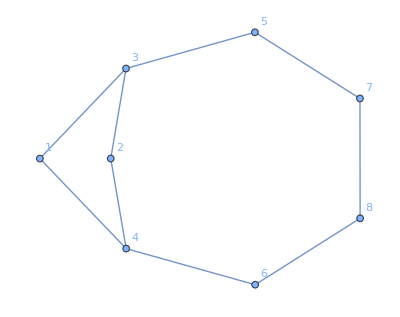

```mathematica
A={
{0,0,1,1,0,0,0,0},
{0,0,1,1,0,0,0,0},
{1,1,0,0,1,0,0,0},
{1,1,0,0,0,1,0,0},
{0,0,1,0,0,0,1,0},
{0,0,0,1,0,0,0,1},
{0,0,0,0,1,0,0,1},
{0,0,0,0,0,1,1,0}
};
AdjacencyGraph[A,VertexLabels->Automatic]
```

## Tree Real Algebraic Roots

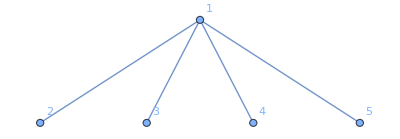

4 λ^3-λ^5

{-2,2,0,0,0}

{{λ^2/(-3 λ+λ^3)}}

```mathematica
T=Graph[{1<->2,1<->3,1<->4,1<->5},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
Eigenvalues[AdjacencyMatrix[T]]
Smash[T,{2}]
```

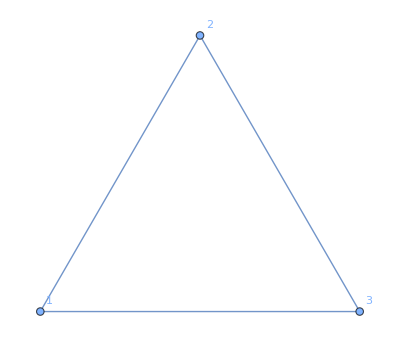

2+3 λ-λ^3

{2,-1,-1}

{{2/(-1+λ)}}

```mathematica
T=Graph[{1<->2,1<->3,2<->3},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
Eigenvalues[AdjacencyMatrix[T]]
Simplify[Smash[T,{2}]]
```

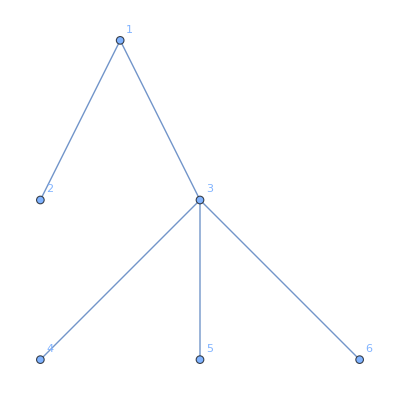

3 λ^2-5 λ^4+λ^6

```mathematica
T=Graph[{1<->2,1<->3,3<->4,3<->5,3<->6},VertexLabels->Automatic]
CharacteristicPolynomial[AdjacencyMatrix[T],λ]
```

## Generalizations Attempts (Equitable Partitions)

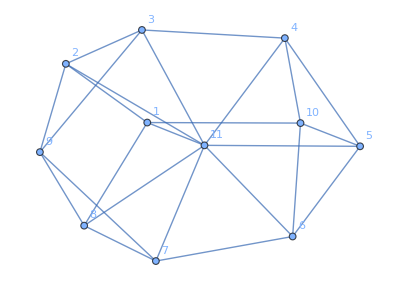

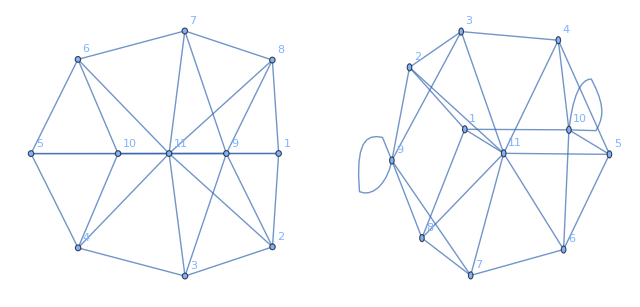

{{(8 (-1+λ))/(-2-3 λ+λ^2)}}

{{λ→1}}

{{(8 (-1+λ))/(-2-3 λ+λ^2)}}

{{λ→1}}

```mathematica
G=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->8,8<->1,2<->9,3<->9,8<->9,7<->9,1<->10,4<->10,5<->10,6<->10,11<->1,11<->2,11<->3,11<->4,11<->5,11<->6,11<->7,11<->8},VertexLabels->Automatic]
A=Normal[AdjacencyMatrix[G]];
A1 = A;
A1[[9,10]]=A1[[9,10]]+1;
A1[[10,9]]=A1[[10,9]]+1;
A2 = A;
A2[[9,9]]=A2[[9,9]]+1;
A2[[10,10]]=A2[[10,10]]+1;
G1 = AdjacencyGraph[A1,VertexLabels->Automatic];
G2=AdjacencyGraph[A2,VertexLabels->Automatic];
GraphicsRow[
{
G1,
G2
}
]
Simplify[Smash[G1,{11}]]
Solve[Simplify[Smash[G1,{11}]][[1,1]]==0,λ]
Simplify[Smash[G2,{11}]]
Solve[Simplify[Smash[G2,{11}]][[1,1]]==0,λ]
```